Dynamical Scheme of Quantum Computation |

Implementation of Single-Qubit Gatespaclet:Q3/tutorial/DynamicalScheme#870548592 | Implementation of CNOT Gatepaclet:Q3/tutorial/DynamicalScheme#477795464

See also Section 4.2 of the Quantum Workbook (Springer, 2022)https://github.com/quantum-mob/QuantumWorkbook.

The dynamical scheme of quantum computation implements the desired quantum gates through a time- evolution operator governing the dynamics of the physical qubits in a quantum computer; hence the name. It is the most common scheme for quantum computation with the majority of quantum computers demonstrated so far based on this scheme. Here, we briefly survey the elementary principles and common methods to achieve elementary single-qubit and two-qubit quantum gates in the dynamical scheme.

CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | The CNOT gate
CZpaclet:Q3/ref/CZQ3 Package Symbol | The CZ gate
SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol | The SWAP gate

Q3 functions related to two-qubits gates.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Implementation of Single-Qubit Gates

Conceptually, the most straightforward way to control a single qubit is to apply the static parameters B^x, B^y, and B^z for a certain period τ of operation time. We refer to them collectively by a vector B=(B^x,B^y,B^z). One can regard it as a fictitious magnetic field, but the dimension of B is energy unlike that for a real magnetic field. The Hamiltonian for the qubit is given by

H=1/2 B·S

where S:=(S^x,S^y,S^z) is the vector of the Pauli operators on the Hilbert space 𝒮. The time evolution is then governed by the unitary operator

U(t)=exp(-ⅈtH)=exp(-ⅈtB·S/2)

in accordance with Postulate 2 of quantum mechanics. It has the same form as the single-qubit rotation operator, describing the rotation in the Bloch space around the axis parallel to the vector B by angle ϕ(t)=|B|t. When the involved two-level system is a true spin, such a rotation in the Bloch space is called the Larmor precession.

Consider a qubit. Let us apply a (fictitious) magnetic field.

```mathematica
Let[Real,B]
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (B_1 S^x+B_2 S^y+B_3 S^z)

To be specific, we consider the case with the magnetic field between the x-  and z-axis in the xz-plane. The factor of 1/√2is to set the energy (frequency) scale to unit.

```mathematica
B[1]=B[3]=1/Sqrt[2];B[2]=0;
opH
```

1/2 (S^x/(√2)+S^z/(√2))

```mathematica
Clear[opU]
opU[t_]=MultiplyExp[-I t opH]
opU[t]//Elaborate
```

ⅇ^(-1/2 ⅈ t (S^x/(√2)+S^z/(√2)))

Cos[t/2]-(ⅈ S^x Sin[t/2])/(√2)-(ⅈ S^z Sin[t/2])/(√2)

```mathematica
Clear[vec]
vec[t_]=opU[t]**Ket[]//Elaborate
```

-(ⅈ 1_S Sin[t/2])/(√2)+0_S (Cos[t/2]-(ⅈ Sin[t/2])/(√2))

This illustrates the Larmor precession (with the qubit regarded as a “spin”).
Technical Note: You need Chop because numerical errors sometimes give 0.+Ket[…], which cannot be handled properly by BlochVector.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

Let us now examine the probabilities for the qubit to be found in the logical basis states.

```mathematica
prob[t_]=Abs[ExpToTrig@Normal@Matrix@vec[t]]^2
```

{(|Cos[t/2]-(ⅈ Sin[t/2])/(√2)|)^2,1/2 (|Sin[t/2]|)^2}

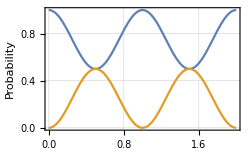

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2πB)","Probability"}]
```

Although conceptually simple, the above method has limited applicability in many practical systems. For example, in the presence of other levels, one cannot apply the method selectively between the two levels in question. A more widely applicable method is to apply an oscillating field. Suppose that

B^x=B_⊥cos(ωt),    B^y=B_⊥ sin(ωt),     B^z=B_0 .

One can regard it as a fictitious magnetic field precessing around the z-axis with
(angular) frequency ω. The Hamiltonian now depends on time, and it is given by

H(t)=1/2 B_⊥[cos(ωt)S^x+sin(ωt)S^y]+1/2 B_0 S^z .

Recalling that the Pauli operators are the generators of rotation, we observe that

U_z^†(ω t)H(t)U_z(ωt)=1/2 B S^x+1/2 B_0 S^z

does not depend on time any longer. This observation suggests that the dynamics look simpler in the rotating frame. Since the rotating frame is not an inertial frame, one has to take into account the non-inertial effect corresponding to the classical inertial force. The state vectors ψ(t) and ψ_R(t) in the lab and rotating frame, respectively, are related by

ψ_R(t)=U_z^†(ωt)ψ(t) .

Putting it into the original Schrödinger equation for ψ(t),

ⅈ∂_t ψ(t)=H(t)ψ(t) ,

and operating U_z^†(ωt) from the left on both sides, one can get the Schrödinger equation in the rotating frame,

ⅈ∂_t ψ_R(t)=H_R(t)ψ_R(t) ,

where the Hamiltonian HˆR in the rotating frame has been defined by

H_R(t):=U_z^†(ω t)H(t)U_z(ωt)-U_z^†(ω t)[ⅈ∂_t U_z(ωt)]=1/2 B S^x+1/2 B_0 S^z.

The second term in H_R is responsible for the non-inertial effect. As already expected in the above observation, the rotating-frame Hamiltonian does not depend on time any longer,

H_R=1/2 B S^x+1/2(B_0-ω)S^z.

The time-evolution operator in the rotating frame,

U_R(t)=exp(-ⅈt H_R)

is formally the same as the one in the lab frame. It describes a precession around the axis parallel to B_R:=(B_⊥,0,B_0−ω) with the frequency

Ω_R:=√(B_⊥^2+(B_0-ω)^2) .

The precession in the rotating frame is called the Rabi oscillation, and the frequency is called the Rabi frequency. The fictitious magnetic field in the rotating frame, B_R, is almost along the x-axis for ω≈B_0. That is, the time-evolution U_R(t) in the rotating frame corresponds to the rotation around the x-axis in the Bloch sphere. In this case, the qubit can make a full transition from the initial state 0 to the orthogonal state 1 by properly tuning the operation time and/or the parameter B_⊥. In this sense, when ω≈B_0, the system is said to be at resonance. As the driving frequency ω gets away off the resonance, the maximum transition probability becomes smaller and smaller. This resonance behavior allows to induce transitions between a selected pair of two levels among many others.

Let us now apply a time-dependent field. It precesses around the z-axis. Note that typically, B_3≫B_1,B_2.

```mathematica
ω=2Pi;
B[1]=Cos[ω t];
B[2]=Sin[ω t];
B[3]=1.1ω; (* near resonance *)
Graphics3D[{Blue,Table[Arrow@Tube@{{0,0,0},B@{1,2,3}},{t,0,1,0.1}]},
PlotRange->ω{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (Cos[2 π t] S^x+6.9115 S^z+S^y Sin[2 π t])

```mathematica
opHR=Rotation[-ω t,S[3]]**opH**Rotation[ω t,S[3]]-ω S[3]/2//Elaborate//Chop
```

S^x/2+0.314159 S^z

```mathematica
opUR[t_]=MultiplyExp[-I t opHR]
```

ⅇ^(-ⅈ t (S^x/2+0.314159 S^z))

```mathematica
Clear[vec]
vec[t_]=opUR[t]**Ket[]//Elaborate;
```

This illustrates the precession in the rotating frame, which is called the Rabi oscillation.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

This shows the transition probabilities in the logical basis states. Note that the probabilities are the same both in the lab and rotating frame. The Rabi oscillation frequency is in this particular example is close to one---it is exactly one at resonance.

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2;
```

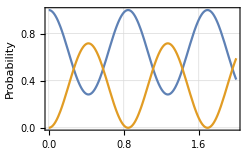

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2π)","Probability"}]
```

Let us consider the case exactly at the resonance.

```mathematica
ω=2Pi;
B[1]=Cos[ω t];
B[2]=Sin[ω t];
B[3]=ω; (* resonance *)
```

```mathematica
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
opHR=Rotation[-ω t,S[3]]**opH**Rotation[ω t,S[3]]-ω S[3]/2//Elaborate//Chop
opUR[t_]=MultiplyExp[-I t opHR]
```

1/2 (Cos[2 π t] S^x+2 π S^z+S^y Sin[2 π t])

S^x/2

ⅇ^(-1/2 ⅈ t S^x)

The Rabi oscillation now corresponds to the Larmor precession around the x-axis in the rotating frame.

```mathematica
Clear[vec]
vec[t_]=opUR[t]**Ket[]//Elaborate;
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

As the precession axis is exactly along the x-axis, the maximum transition probability can reach unity.

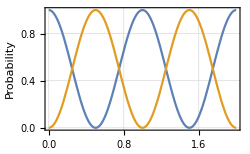

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2;
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2π)","Probability"}]
```

In the above discussion of a Rabi oscillation, the two parameters are deliberately manipulated periodically with a relative phase difference of π/2. This may not always be possible in practical experiments, but fortunately, the requirement is not so stringent. Suppose that only one parameter can be driven periodically, say, B^y(t) = 2 B_⊥ sin(ωt) (notice the factor of 2 introduced here for convenience). The time-dependent Hamiltonian

H(t)=1/2 B_⊥sin(ωt)S^y+1/2 B_0 S^z

looks seemingly simpler than the one for the perfect Rabi oscillation, but it does not allow for an exact solution. Instead, let us rewrite it into the form

H(t)=1/2 B_0 S^z+1/2 B_⊥[cos(ωt)S^x+sin(ωt)S^y]-1/2 B_⊥[cos(-ωt)S^x+sin(-ωt)S^y] ,

which is obviously the same as the above Hamiltonian. While the second term describes a fictitious magnetic field rotating in the counterclockwise direction, the field in the last term rotates in the clockwise direction. In the frame rotating in the counterclockwise sense, the Hamiltonian reads as

H_R=1/2(B_0-ω)S^z+1/2 B S^x-1/2 B_⊥[cos(-2ωt)S^x+sin(-2ωt)S^y].

The first two terms describe the Rabi oscillation discussed above. On the other hand, the last term oscillates fast with frequency 2ω, which is typically much larger than the Rabi frequency Ω_R. Such an oscillation is therefore too fast for the system to respond to, and its effect is negligible as the typical time scale of the system is fixed by the Rabi frequency Ω_R. On this ground, assuming ω≈B_0, one often drops the fast oscillating term from the Hamiltonian so that

H(t)=1/2 B_⊥sin(ωt)S^y+1/2 B_0 S^z≈1/2 B_⊥[cos(ωt)S^x+sin(ωt)S^y]+1/2 B_0 S^z .

Such an approximation is called the rotating-wave approximation. The approximation is valid as long as B_0≫Ω_R.

H(t)=1/2 B_⊥[cos(ωt)S^x+sin(ωt)S^y]+1/2 B_0 S^z .

Implementation of CNOT Gate

The CNOT gate is a vital gate operation for any quantum algorithm. It is seemingly simple, yet it is not trivial to physically implement in a practical system. A typical obstacle is that the Hamiltonian, in particular the coupling between two qubits, is restricted to certain limited forms. Here we take a few examples of the qubit-qubit interaction and see how one can use it to implement the CNOT gate. These examples provide a general idea of what is required to implement CNOT or similar gates in a given practical physical system.

One of the most common forms of the exchange interaction between two qubits is the so-called Heisenberg exchange interaction

H=J(S_1^X S_2^X+S_1^Y S_2^Y+S_1^Z S_2^Z) .

As one can see from its matrix representation

H≐J (1 | 0 | 0 | 0
0 | -1 | 2 | 0
0 | 2 | -1 | 0
0 | 0 | 0 | 1) ,

it operates nontrivially only within the subspace spanned by |01⟩ and |10⟩ just like the SWAP gate. This is because the Heisenberg exchange coupling conserves the total angular momentum. More explicitly, up to a constant shift and multiplication factor, the Heisenberg exchange Hamiltonian equals the SWAP gate

(H+J)/(2J)≐(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)≐SWAP .

The SWAP gate behaves like the NOT gate within the subspace spanned by |01⟩ and |10⟩. Hence, the rotation around the x-axis (in the Bloch space corresponding to the subspace) by angle π results in the NOT gate. This implies that by tuning the exchange coupling constant and the operation time τ such that Jτ=π/4 will achieve the SWAP gate (Loss and DiVincenzo, 1998https://doi.org/10.1103/PhysRevA.57.120)

SWAP=exp[-ⅈπ/4(S_1^X S_2^X+S_1^Y S_2^Y+S_1^Z S_2^Z-1)] .

The SWAP gate itself is not universal. The limitation originates from the fact that the Heisenberg exchange interaction conserves the total angular momentum. However, the √SWAP gate is universal. One can construct the CZ gate by combining the √SWAP gate with single-qubit gates. It takes two additional Hadamard gates to construct the CNOT gate from the CZ gate (see the “Two-Qubit Gates” tutorial).

Summing up, when the Heisenberg exchange interaction is available in a system of qubits, one can achieve the CZ gate using two √SWAP gates and three single- qubit gates. If desired, one can apply two additional Hadamard gates to implement the CNOT gate.

Consider the Heisenberg exchange coupling.

```mathematica
op=MultiplyDot[S[1,All],S[2,All]]
```

S_1^xS_2^x+S_1^yS_2^y+S_1^zS_2^z

This is the matrix representation.

```mathematica
mat=Matrix[(1+op)/2];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
opU=MultiplyExp[-I (Pi/4)*(op-1)]
opU//Elaborate
```

ⅇ^(-1/4 ⅈ π (-1+S_1^xS_2^x+S_1^yS_2^y+S_1^zS_2^z))

1/2+1/2 S_1^xS_2^x+1/2 S_1^yS_2^y+1/2 S_1^zS_2^z

```mathematica
matU=Matrix[opU];
matU//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

There are two additional types of qubit-qubit exchange interactions, the XY and Ising exchange interactions. The XY exchange interaction (also known as the planar exchange interaction) is described by the Hamiltonian

H=J(S_1^X S_2^X+S_1^Y S_2^Y) .

The matrix representation

H≐J (1 | 0 | 0 | 0
0 | 0 | 2 | 0
0 | 2 | 0 | 0
0 | 0 | 0 | 1) ,

suggests that one can use the XY exchange interaction in essentially the same way as for the Heisenberg exchange interaction. An explicit construction is left for an exercise.

Next, consider the XY exchange interaction.

```mathematica
op=MultiplyDot[S[1,{1,2}],S[2,{1,2}]]
```

S_1^xS_2^x+S_1^yS_2^y

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 2 | 0
0 | 2 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
opU=MultiplyExp[-I ϕ op]
```

ⅇ^(-ⅈ ϕ (S_1^xS_2^x+S_1^yS_2^y))

```mathematica
Matrix[opU]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 ϕ] | -ⅈ Sin[2 ϕ] | 0
0 | -ⅈ Sin[2 ϕ] | Cos[2 ϕ] | 0
0 | 0 | 0 | 1)

The Ising exchange interaction has the Hamiltonian

H=J S_1^Z S_2^Z ,

where the z-component has no special meaning. Replacing the z-component with the x- or y-component has the same effect. The Ising exchange interaction allows for a more direct implementation of the CZ gate. Though a direct investigation is sufficient, let us here take another view of the CZ gate for heuristic purposes. Recall that the CZ gate is defined as

CZ=Σ_(x=0,1)xx⊗Z^x=ⅈ Σ_(x=0,1)xx⊗ⅇ^(-ⅈπxZ/2) .

Since x=0,1 are the eigenvalues of 11= (I−Z)/2,

CZ=ⅇ^(iπ/4)exp[-ⅈπ/4(Z⊗I+I⊗Z-Z⊗Z)] .

We note that the exponent involves the Ising exchange interaction between the two qubits. Therefore, one can implement the CZ gate with the first and second qubits as the control and target qubits, respectively, in terms of the Hamiltonian
(up to an irrelevant global phase factor ⅇ^(ⅈπ/4)) of the form

H=B(S_1^Z+S_2^Z)-J S_1^Z S_2^Z .

Note that the exchange coupling (apart from the single-qubit term) is of the Ising type. Putting B=J, the time-evolution operator governed by the Hamiltonian is given by

U(t)=exp[-ⅈJt(S_1^Z+S_2^Z-J S_1^Z S_2^Z)] .

Therefore, the CZ gate is achieved by tuning the parameters B and J and the operation time such that

Jτ=Bτ=π/4.

Let us now consider the Ising exchange interaction (in the dimensionless form). Here, we have introduced an additional single-qubit term controlling the second qubit. Note that the Hamiltonian is symmetric about the two qubits.

```mathematica
op= S[1,3]+ S[2,3]- S[1,3]**S[2,3];
op//PauliForm
```

I⊗Z+Z⊗I-Z⊗Z

Calculate the matrix representation of the Hamiltonian.

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -3)

Take a look at the time-evolution operator at a (dimensionless) time ϕ.

```mathematica
opU=MultiplyExp[-I ϕ op]
opU//Matrix//MatrixForm
```

ⅇ^(-ⅈ ϕ (-S_1^ZS_2^Z+S_1^Z+S_2^Z))

(ⅇ^(-ⅈ ϕ) | 0 | 0 | 0
0 | ⅇ^(-ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(3 ⅈ ϕ))

Now, it is clear that we can achieve the CZ gate by setting ϕ=π/4.

```mathematica
opU=Exp[I Pi/4] MultiplyExp[-I (Pi/4) op]
opU//Matrix//MatrixForm
```

ⅇ^((ⅈ π)/4) ⅇ^(-1/4 ⅈ π (-S_1^ZS_2^Z+S_1^Z+S_2^Z))

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Models
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪D. Loss and D. DiVincenzo, Physical Review A 57, 120 (1998)https://doi.org/10.1103/PhysRevA.57.120, "Quantum computation with quantum dots."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).